```mathematica
(* Number of equivalent monthly vacation days *)
```

```mathematica
data = {{1,8/24}, {7,2/7}, {365, 24/365}}; (* 8 hours of sleep per day, 2 weekend days per week, 24 working days per year *)
```

```mathematica
model  = a + b ⅇ^(-c x);
```

```mathematica
fit = FindFit[data,model,{a,b,c},x]
```

{a→0.0657516,b→0.276466,c→0.0326612}

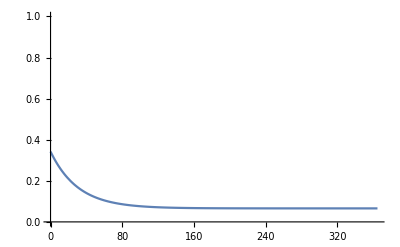

```mathematica
Plot[model/.fit, {x, 0, 365}, PlotRange-> {0, 1}]
```

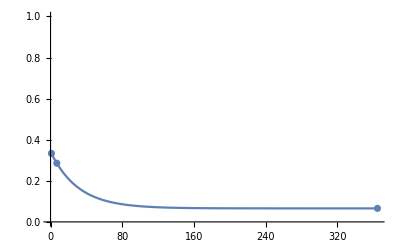

```mathematica
Show[%, ListPlot[data]]
```

```mathematica
30 model/.fit/.x-> 30
```

5.08588

```mathematica
(* That's 5 (five) working days per month holidays. *)
```